```mathematica
SetDirectory["C:\\Users\\Ксения\\palabos\\examples\\showCases\\boundaryCondition\\tmp"]
```

C:\Users\Ксения\palabos\examples\showCases\boundaryCondition\tmp

```mathematica
a= Import["dens_en.dat"]
```

{{5000,0.4999,1.,0.0000160122},{10000,0.9999,1.,0.0000167219},{15000,1.4999,1.,0.0000167489},{20000,1.9999,1.,0.00001675},{25000,2.4999,1.,0.00001675},{30000,2.9999,1.,0.00001675},{35000,3.4999,1.,0.00001675},{40000,3.9999,1.,0.00001675},{45000,4.4999,1.,0.00001675},{50000,4.9999,1.,0.00001675},{55000,5.4999,1.,0.00001675},{60000,5.9999,1.,0.00001675},{65000,6.4999,1.,0.00001675},{70000,6.9999,1.,0.00001675},{75000,7.4999,1.,0.00001675},{80000,7.9999,1.,0.00001675},{85000,8.4999,1.,0.00001675},{90000,8.9999,1.,0.00001675},{95000,9.4999,1.,0.00001675},{100000,9.9999,1.,0.00001675},{105000,10.4999,1.,0.00001675},{110000,10.9999,1.,0.00001675},{115000,11.4999,1.,0.00001675},{120000,11.9999,1.,0.00001675},{125000,12.4999,1.,0.00001675},{130000,12.9999,1.,0.00001675},{135000,13.4999,1.,0.00001675},{140000,13.9999,1.,0.00001675},{145000,14.4999,1.,0.00001675},{150000,14.9999,1.,0.00001675},{155000,15.4999,1.,0.00001675},{160000,15.9999,1.00001,0.00001675},{165000,16.4999,1.00001,0.00001675},{170000,16.9999,1.00001,0.00001675},{175000,17.4999,1.00001,0.00001675},{180000,17.9999,1.00001,0.00001675},{185000,18.4999,1.00001,0.00001675},{190000,18.9999,1.00001,0.00001675},{195000,19.4999,1.00001,0.00001675},{200000,19.9999,1.00001,0.00001675},{205000,20.4999,1.00001,0.00001675},{210000,20.9999,1.00001,0.00001675},{215000,21.4999,1.00001,0.00001675},{220000,21.9999,1.00001,0.00001675},{225000,22.4999,1.00001,0.00001675},{230000,22.9999,1.00001,0.00001675},{235000,23.4999,1.00001,0.00001675},{240000,23.9999,1.00001,0.00001675},{245000,24.4999,1.00001,0.00001675},{250000,24.9999,1.00001,0.00001675},{255000,25.4999,1.00001,0.00001675},{260000,25.9999,1.00001,0.00001675},{265000,26.4999,1.00001,0.00001675},{270000,26.9999,1.00001,0.00001675},{275000,27.4999,1.00001,0.00001675},{280000,27.9999,1.00001,0.00001675},{285000,28.4999,1.00001,0.00001675},{290000,28.9999,1.00001,0.00001675},{295000,29.4999,1.00001,0.00001675},{300000,29.9999,1.00001,0.00001675},{305000,30.4999,1.00001,0.00001675},{310000,30.9999,1.00001,0.00001675},{315000,31.4999,1.00001,0.00001675},{320000,31.9999,1.00001,0.00001675},{325000,32.4999,1.00001,0.00001675},{330000,32.9999,1.00001,0.00001675},{335000,33.4999,1.00001,0.00001675},{340000,33.9999,1.00001,0.00001675},{345000,34.4999,1.00001,0.00001675},{350000,34.9999,1.00001,0.00001675},{355000,35.4999,1.00001,0.00001675},{360000,35.9999,1.00001,0.00001675},{365000,36.4999,1.00001,0.00001675},{370000,36.9999,1.00001,0.00001675},{375000,37.4999,1.00001,0.00001675},{380000,37.9999,1.00001,0.00001675},{385000,38.4999,1.00001,0.00001675},{390000,38.9999,1.00001,0.00001675},{395000,39.4999,1.00001,0.00001675},{400000,39.9999,1.00001,0.00001675},{405000,40.4999,1.00001,0.00001675},{410000,40.9999,1.00001,0.00001675},{415000,41.4999,1.00001,0.00001675},{420000,41.9999,1.00001,0.00001675},{425000,42.4999,1.00001,0.00001675},{430000,42.9999,1.00001,0.00001675},{435000,43.4999,1.00001,0.00001675},{440000,43.9999,1.00001,0.00001675},{445000,44.4999,1.00001,0.00001675},{450000,44.9999,1.00001,0.00001675},{455000,45.4999,1.00001,0.00001675},{460000,45.9999,1.00001,0.00001675},{465000,46.4999,1.00001,0.00001675},{470000,46.9999,1.00001,0.00001675},{475000,47.4999,1.00001,0.00001675},{480000,47.9999,1.00001,0.00001675},{485000,48.4999,1.00001,0.00001675},{490000,48.9999,1.00002,0.00001675},{495000,49.4999,1.00002,0.00001675},{500000,49.9999,1.00002,0.00001675},{505000,50.4999,1.00002,0.00001675},{510000,50.9999,1.00002,0.00001675},{515000,51.4999,1.00002,0.00001675},{520000,51.9999,1.00002,0.00001675},{525000,52.4999,1.00002,0.00001675},{530000,52.9999,1.00002,0.00001675},{535000,53.4999,1.00002,0.00001675},{540000,53.9999,1.00002,0.00001675},{545000,54.4999,1.00002,0.00001675},{550000,54.9999,1.00002,0.00001675},{555000,55.4999,1.00002,0.00001675},{560000,55.9999,1.00002,0.00001675},{565000,56.4999,1.00002,0.00001675},{570000,56.9999,1.00002,0.00001675},{575000,57.4999,1.00002,0.00001675},{580000,57.9999,1.00002,0.00001675},{585000,58.4999,1.00002,0.00001675},{590000,58.9999,1.00002,0.00001675},{595000,59.4999,1.00002,0.00001675},{600000,59.9999,1.00002,0.00001675},{605000,60.4999,1.00002,0.00001675},{610000,60.9999,1.00002,0.00001675},{615000,61.4999,1.00002,0.00001675},{620000,61.9999,1.00002,0.00001675},{625000,62.4999,1.00002,0.00001675},{630000,62.9999,1.00002,0.00001675},{635000,63.4999,1.00002,0.00001675},{640000,63.9999,1.00002,0.00001675},{645000,64.4999,1.00002,0.00001675},{650000,64.9999,1.00002,0.00001675},{655000,65.4999,1.00002,0.00001675},{660000,65.9999,1.00002,0.00001675},{665000,66.4999,1.00002,0.00001675},{670000,66.9999,1.00002,0.00001675},{675000,67.4999,1.00002,0.00001675},{680000,67.9999,1.00002,0.00001675},{685000,68.4999,1.00002,0.00001675},{690000,68.9999,1.00002,0.00001675},{695000,69.4999,1.00002,0.00001675},{700000,69.9999,1.00002,0.00001675},{705000,70.4999,1.00002,0.00001675},{710000,70.9999,1.00002,0.00001675},{715000,71.4999,1.00002,0.00001675},{720000,71.9999,1.00002,0.00001675},{725000,72.4999,1.00002,0.00001675},{730000,72.9999,1.00002,0.00001675},{735000,73.4999,1.00002,0.00001675},{740000,73.9999,1.00002,0.00001675},{745000,74.4999,1.00002,0.00001675},{750000,74.9999,1.00002,0.00001675},{755000,75.4999,1.00002,0.00001675},{760000,75.9999,1.00002,0.00001675},{765000,76.4999,1.00002,0.00001675},{770000,76.9999,1.00002,0.00001675},{775000,77.4999,1.00002,0.00001675},{780000,77.9999,1.00002,0.00001675},{785000,78.4999,1.00002,0.00001675},{790000,78.9999,1.00002,0.00001675},{795000,79.4999,1.00002,0.00001675},{800000,79.9999,1.00002,0.00001675},{805000,80.4999,1.00002,0.00001675},{810000,80.9999,1.00002,0.00001675},{815000,81.4999,1.00002,0.00001675},{820000,81.9999,1.00003,0.00001675},{825000,82.4999,1.00003,0.00001675},{830000,82.9999,1.00003,0.00001675},{835000,83.4999,1.00003,0.00001675},{840000,83.9999,1.00003,0.00001675},{845000,84.4999,1.00003,0.00001675},{850000,84.9999,1.00003,0.00001675},{855000,85.4999,1.00003,0.00001675},{860000,85.9999,1.00003,0.00001675},{865000,86.4999,1.00003,0.00001675},{870000,86.9999,1.00003,0.00001675},{875000,87.4999,1.00003,0.00001675},{880000,87.9999,1.00003,0.00001675},{885000,88.4999,1.00003,0.00001675},{890000,88.9999,1.00003,0.00001675},{895000,89.4999,1.00003,0.00001675},{900000,89.9999,1.00003,0.00001675},{905000,90.4999,1.00003,0.00001675},{910000,90.9999,1.00003,0.00001675},{915000,91.4999,1.00003,0.00001675},{920000,91.9999,1.00003,0.00001675},{925000,92.4999,1.00003,0.00001675},{930000,92.9999,1.00003,0.00001675},{935000,93.4999,1.00003,0.00001675},{940000,93.9999,1.00003,0.00001675},{945000,94.4999,1.00003,0.00001675},{950000,94.9999,1.00003,0.00001675},{955000,95.4999,1.00003,0.00001675},{960000,95.9999,1.00003,0.00001675},{965000,96.4999,1.00003,0.00001675},{970000,96.9999,1.00003,0.00001675},{975000,97.4999,1.00003,0.00001675},{980000,97.9999,1.00003,0.00001675},{985000,98.4999,1.00003,0.00001675},{990000,98.9999,1.00003,0.00001675},{995000,99.4999,1.00003,0.00001675},{1000000,99.9999,1.00003,0.00001675}}

```mathematica
a=Transpose[a];
```

```mathematica
rho={};
i= 1;
While[i<200,AppendTo[rho,{a[[2,i]],a[[3,i]]-1}];i+=4]
(*For[i=1,i<200,i++;AppendTo[rho,{a[[2,i]],a[[3,i]]-1}]]*)
```

```mathematica
en={};
For[i=1,i<200,i++;AppendTo[en,{a[[2,i]],a[[4,i]]}]]
```

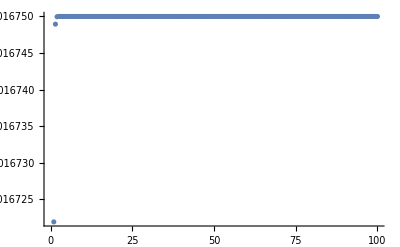

```mathematica
ListPlot[en]
```

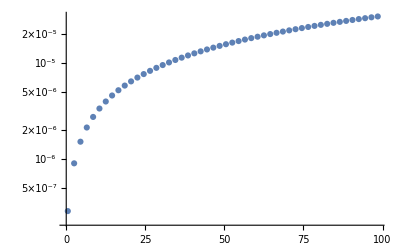

```mathematica
ListLogPlot[rho]
```

```mathematica
Show[%44,AxesStyle->Black]
```

-Graphics-

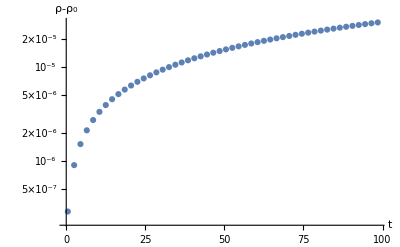

```mathematica
Show[%45,AxesLabel->{HoldForm[t],HoldForm[ρ-Subscript[ρ, 0]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0],Bold}]
```

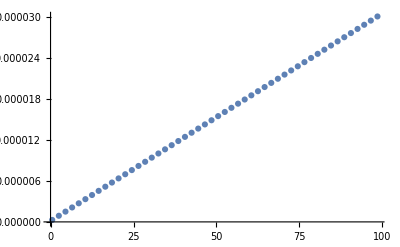

```mathematica
Show[%40,AxesStyle->Black]
```

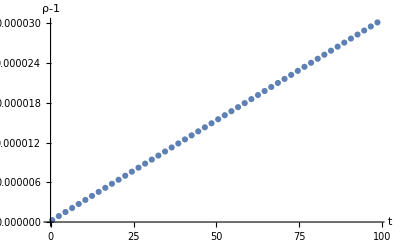

```mathematica
Show[%41,AxesLabel->{HoldForm[t],HoldForm[ρ-1]},PlotLabel->None,LabelStyle->{10,GrayLevel[0],Bold}]
```